# MATH224: Homework 7

## Plots all made by Trevor Swan.

NOTE: Please Indicate the which graph is which on the x(t) and y(t) graphs. If you ever doubt formatting, check the textbook solutions and use them as a reference.

## Question 3.6.13

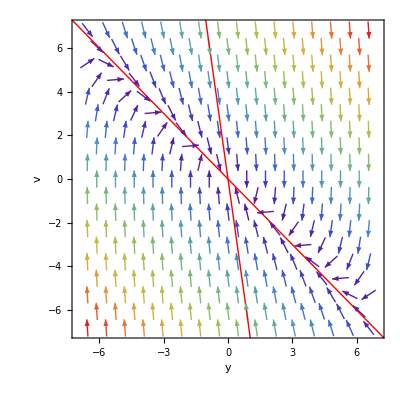

```mathematica
(* Set up Eigenvectors for part c *)
parentPlot =VectorPlot[{0*x+1*y,-7*x+-8*y},{x,-7,7},{y,-7,7},VectorPoints->Medium,Axes->True,AxesLabel->{"y","v"},VectorColorFunction->"Rainbow"];
eigenVectors=Eigenvectors[{{0,1},{-7,-8}}];
eigenLines1=Graphics[{Red,Arrowheads[0],Arrow[{{0,0},#}]&/@(10*eigenVectors)}];
eigenLines2 = Graphics[{Red,Arrowheads[0],Arrow[{{0,0},#}]&/@(-10*eigenVectors)}];
(* Display the plot for c *)
Show[parentPlot,eigenLines1, eigenLines2, PlotRange-> {{-7,7},{-7,7}}]
```

## Question 3.6.13

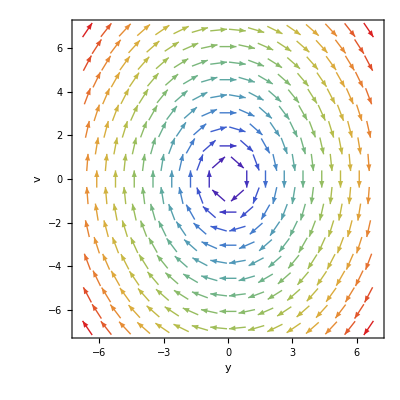

```mathematica
(* Set up Eigenvectors for part c *)
parentPlot =VectorPlot[{0*x+1*y,-1.5*x+0*y},{x,-7,7},{y,-7,7},VectorPoints->Medium,Axes->True,AxesLabel->{"y","v"},VectorColorFunction->"Rainbow"];
(* Display the plot for c *)
Show[parentPlot, PlotRange-> {{-7,7},{-7,7}}]
```